### Equation

```mathematica
ψ
```

ψ

```mathematica
ODE=Function[{r,l,S},D[ψ[r],{r,2}]+2/r D[ψ[r],{r,1}]-l(l+1)/r^2 ψ[r]==S[l]]
```

Function[{r,l,S},∂_{r,2} ψ[r]+(2 ∂_{r,1} ψ[r])/r-(l (l+1) ψ[r])/r^2==S[l]]

```mathematica
ODE[r,0,S]
```

(2 ψ'[r])/r+ψ''[r]==S[0]

### Source

```mathematica
Source=Function[{r,θ,z0}, 1/(r^2+z0^2-2z0 r Cos[θ])^(1/2)]
```

Function[{r,θ,z0},1/(√(r^2+z0^2-2 z0 r Cos[θ]))]

```mathematica
S3D=Function[{x,y,z,z0},1/((x^2+y^2+(z-z0)^2)^(1/2))]
```

Function[{x,y,z,z0},1/(√(x^2+y^2+(z-z0)^2))]

```mathematica
S3D[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ],z0d]//FullSimplify
```

1/(√(r^2+z0d^2-2 r z0d Cos[θ]))

```mathematica
Source[r,θ,z0d]-S3D[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ],z0d]//FullSimplify
```

0

```mathematica
Source[z0,1,z0]
```

1/(√(2 z0^2-2 z0^2 Cos[1]))

```mathematica
Source[z0,0.1,z0]
```

10.0042/(√(z0^2))

```mathematica
rho=Function[{a,b,θ},1/(a(1-b Cos[θ]))^(1/2)]
```

Function[{a,b,θ},1/(√(a (1-b Cos[θ])))]

```mathematica
afunc=r^2+z0^2
```

r^2+z0^2

```mathematica
D[afunc, r]
```

2 r

```mathematica
bfunc=2z0 Abs[r]/afunc
```

(2 z0 Abs[r])/(r^2+z0^2)

```mathematica
bfuncNoAbs=2z0 r/afunc
```

(2 r z0)/(r^2+z0^2)

```mathematica
rho[afunc,bfunc,θ]//FullSimplify
```

1/(√(r^2+z0^2-2 z0 Abs[r] Cos[θ]))

```mathematica
rho[a,b,θ]
```

1/(√(a (1-b Cos[θ])))

```mathematica
SAnalyticmodes[l_Integer]:=Module[{prefactor,integrand},(*The 2π and Spherical Harmonic constants simplify to this prefactor*)prefactor=Sqrt[(Pi (2 l+1))/a];
(*The fully algebraic integrand using Legendre Polynomials*)integrand=LegendreP[l,x]/Sqrt[1-b x];
(*Evaluate and simplify*)prefactor*Integrate[integrand,{x,-1,1},Assumptions->{a>0,-1<b<1}]//FullSimplify]
```

```mathematica
S0=SAnalyticmodes[0]
```

(2 √(1/a) (-√(1-b)+√(1+b)) √π)/b

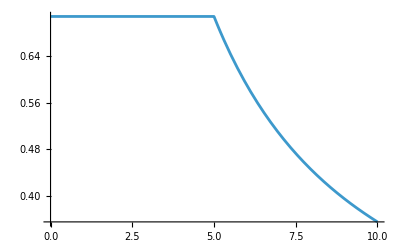

```mathematica
Plot[S0/.{a->afunc,b->bfuncNoAbs}/.z0->5,{r,0,10}]
```

```mathematica
S1=SAnalyticmodes[1]
```

-(2 √(1/a) (2 (√(1-b)-√(1+b))+b (√(1-b)+√(1+b))) √(π/3))/b^2

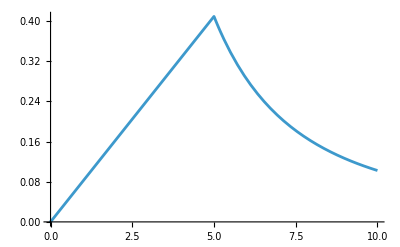

```mathematica
Plot[S1/.{a->afunc,b->bfuncNoAbs}/.z0->5,{r,0,10}]
```

```mathematica
S2=SAnalyticmodes[2]
```

(√(1/a) (-8 √(1-b)+8 √(1+b)+2 b^2 (√(1-b)-√(1+b))-4 b (√(1-b)+√(1+b))) √(π/5))/b^3

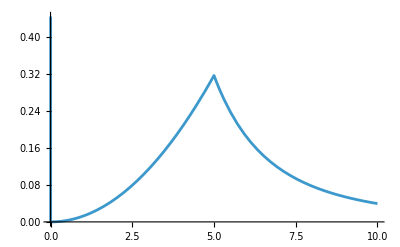

```mathematica
Plot[S2/.{a->afunc,b->bfuncNoAbs}/.z0->5,{r,0,10}]
```

### Replace square roots with Heaviside functions

```mathematica
(*1. Substitute the coordinate functions*)s0Subbed=S0/. {a->afunc,b->bfuncNoAbs};

(*2. Force Mathematica to factor the terms and resolve the absolute values*)
s0Abs=Simplify[s0Subbed,Assumptions->{r∈Reals,z0∈Reals}];

(*3. Write a new rule that targets the Abs[] function instead of Sqrt*)
absToHeavisideRule=Abs[x_]:>x*(2 HeavisideTheta[x]-1);

(*4. Apply the rule*)
s0Heaviside=s0Abs/. absToHeavisideRule
```

(√π (-((r-z0) (-1+2 HeavisideTheta[r-z0]))+(r+z0) (-1+2 HeavisideTheta[r+z0])))/(r z0)

```mathematica
s0Heaviside//Simplify
```

(2 √π (-z0+(-r+z0) HeavisideTheta[r-z0]+(r+z0) HeavisideTheta[r+z0]))/(r z0)

```mathematica
ToHeaviside[f_]:=Module[{fSubbed,fAbs,fHeaviside},(*1. Substitute the coordinate functions*)fSubbed=f/. {a->afunc,b->bfuncNoAbs};
(*2. Force Mathematica to factor into absolute values*)fAbs=Simplify[fSubbed,Assumptions->{r∈Reals,z0∈Reals}];
(*3. Apply the rule (Make sure absToHeavisideRule is already defined in your notebook)*)fHeaviside=fAbs/. absToHeavisideRule;
(*4. Return the final result*)fHeaviside//Simplify]
```

```mathematica
ToHeaviside[S0]
```

(2 √π (-z0+(-r+z0) HeavisideTheta[r-z0]+(r+z0) HeavisideTheta[r+z0]))/(r z0)

```mathematica
ToHeaviside[S1]
```

(2 √(π/3) (-z0^3+(-r^3+z0^3) HeavisideTheta[r-z0]+(r^3+z0^3) HeavisideTheta[r+z0]))/(r^2 z0^2)

```mathematica
ToHeaviside[S2]
```

(2 √(π/5) (-z0^5+(-r^5+z0^5) HeavisideTheta[r-z0]+(r^5+z0^5) HeavisideTheta[r+z0]))/(r^3 z0^3)